Mathematica 函数学习

## 符号表达式

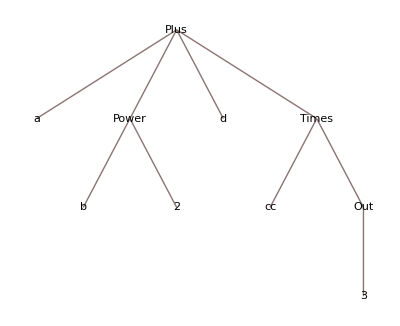

```mathematica
TreeForm[a+b^2+cc%3+d]
```

```mathematica
{x,x^2,y,z}/.{x->1,y->100}
```

{1,1,100,z}

->和:>的区别：

```mathematica
{x,x,x,x}/.x->RandomReal[]
```

{0.403565,0.403565,0.403565,0.403565}

```mathematica
{x,x,x,x}/.x:>RandomReal[]
```

{0.26327,0.0942249,0.0429153,0.74538}

定义函数：

```mathematica
f[x_]:=(x+1)^2
```

```mathematica
{f[1],f[a+b c]}
```

{4,(1+a+b c)^2}

## 列表与表达式操作

```mathematica
List[a,b,c,d]
```

{a,b,c,d}

```mathematica
ragged={{1,2,3},{4,5},{6}};
ragged[[All,1]]
```

{1,4,6}

```mathematica
PadRight[ragged]
```

{{1,2,3},{4,5,0},{6,0,0}}

```mathematica
PadLeft[ragged]
```

{{1,2,3},{0,4,5},{0,0,6}}

```mathematica
Range[4,-10,-3]
```

{4,1,-2,-5,-8}

```mathematica
Array[f,4]
```

{f[1],f[2],f[3],f[4]}

```mathematica
Array[2^#&,4]
```

{2,4,8,16}